```mathematica
Module[
{tail, pow3,runLength,  x, valueTail, allTwos},
For[tail=0,tail <= 8,tail++,
allTwos=IntegerPart[N[Sum[2*3^n,{n,0,tail}]]];
pow3=3^(tail+1);
runLength=2 * 3^tail;
For[x=0, x<runLength,x++,
valueTail=Mod[2^x,pow3];
If [valueTail==allTwos,
Print[{"found",tail, x, valueTail}];
Break[];
]
]
]
]
```

{found,0,1,2}

{found,1,3,8}

{found,2,9,26}

{found,3,27,80}

{found,4,81,242}

{found,5,243,728}

{found,6,729,2186}

{found,7,2187,6560}

{found,8,6561,19682}

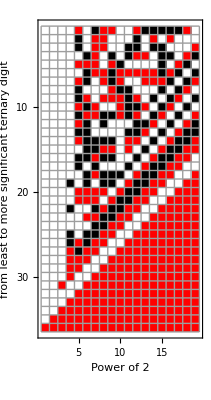

```mathematica
Module[
{ max3=18},
Monitor[
ArrayPlot[Transpose[Table[
With[{keep=Take[PadLeft[IntegerDigits[Mod[2^(3^i),3^(max3*2)],3],max3*2],max3*2]},
keep
],{i,0,max3}]], Frame->True, FrameTicks->Automatic, Mesh->All, ColorRules->{0->White,1->Black,2->Red},FrameLabel->{"from least to more significant ternary digit", "Power of 2"} ,
PlotLabel->GraphicsRow[{Text[  "Worst tail at "] , TraditionalForm[2^(3^i)]}, Spacings->0, AspectRatio->0.2]]
,i]
]
```

```mathematica
IntegerLength[2^(3^15),3]
```

9053153

```mathematica
Module[
{ max3=8},
Table[
(3^i),{i,0,max3}]
]
```

{1,3,9,27,81,243,729,2187,6561}

```mathematica
IntegerDigits[2^81,3]
```

{1,0,1,0,0,2,2,1,0,2,0,1,1,2,2,2,2,1,1,0,2,0,2,1,1,2,1,2,1,2,0,1,1,0,0,2,2,0,0,0,0,2,1,2,2,0,0,2,2,2,2,2}

```mathematica
Module[
{tail, pow3,runLength,  x, valueTail, allTwos},
For[tail=0,tail <= 8,tail++,
allTwos=IntegerPart[N[Sum[2*3^n,{n,0,tail}]]];
pow3=3^(tail+1);
runLength=2 * 3^tail;
For[x=0, x<runLength,x++,
valueTail=Mod[2^x,pow3];
If [valueTail==allTwos,
Print[{"found",tail, x, valueTail}];
Break[];
]
]
]
]
```

```mathematica
Module[
{tail, pow3,runLength,  x, valueTail, allTwos},
For[tail=0,tail <= 8,tail++,
allTwos=IntegerPart[N[Sum[3^n,{n,0,tail}]]];
pow3=3^(tail+1);
runLength=2 * 3^tail;
For[x=0, x<runLength,x++,
valueTail=Mod[2^x,pow3];
If [valueTail==allTwos,
Print[{"found",tail, x, valueTail}];
Break[];
]
]
]
]
```

{found,0,0,1}

{found,1,2,4}

{found,2,8,13}

{found,3,26,40}

{found,4,80,121}

{found,5,242,364}

{found,6,728,1093}

{found,7,2186,3280}

{found,8,6560,9841}

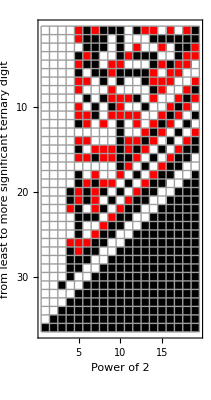

```mathematica
Module[
{ max3=18},
Monitor[
ArrayPlot[Transpose[Table[
With[{keep=Take[PadLeft[IntegerDigits[Mod[2^(3^i-1),3^(max3*2)],3],max3*2],max3*2]},
keep
],{i,0,max3}]], Frame->True, FrameTicks->Automatic, Mesh->All, ColorRules->{0->White,1->Black,2->Red},FrameLabel->{"from least to more significant ternary digit", "Power of 2"} ,
PlotLabel->GraphicsRow[{Text[  "Tail of digit 1 at "] , TraditionalForm[2^(3^i-1)]}, Spacings->0, AspectRatio->0.2]]
,i]
]
```

```mathematica
Module[
{tail, pow3,runLength,  x, valueTail, allTwos},
For[tail=0,tail <= 8,tail++,
allTwos=IntegerPart[N[Sum[3^n,{n,0,tail,2}]]];
pow3=3^(tail+1);
runLength=2 * 3^tail;
For[x=0, x<runLength,x++,
valueTail=Mod[2^x,pow3];
If [valueTail==allTwos,
Print[{"found",tail, x, valueTail}];
Break[];
]
]
]
]
```

{found,0,0,1}

{found,1,0,1}

{found,2,6,10}

{found,3,24,10}

{found,4,78,91}

{found,5,240,91}

{found,6,726,820}

{found,7,2184,820}

{found,8,6558,7381}

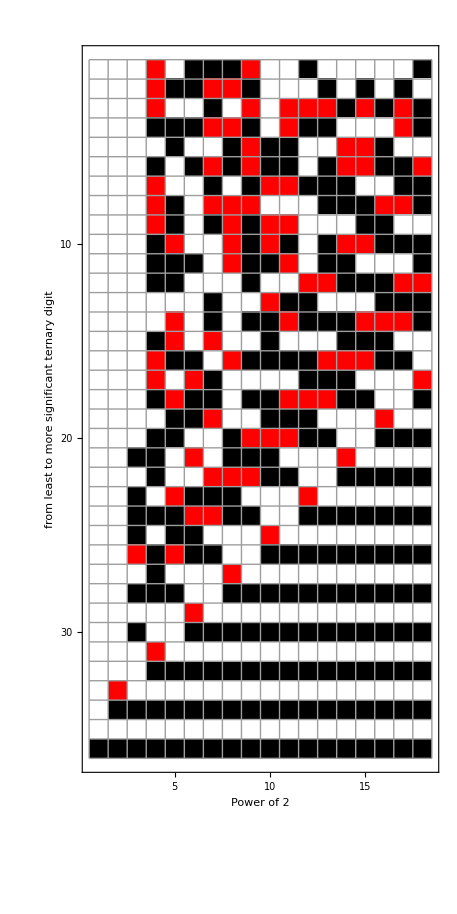

```mathematica
Module[
{ max3=18},
Monitor[
ArrayPlot[Transpose[Table[
With[{keep=Take[PadLeft[IntegerDigits[Mod[2^(3^i-3),3^(max3*2)],3],max3*2],max3*2]},
keep
],{i,1,max3}]], Frame->True, FrameTicks->Automatic, Mesh->All, ColorRules->{0->White,1->Black,2->Red},FrameLabel->{"from least to more significant ternary digit", "Power of 2"} ,
PlotLabel->GraphicsRow[{Text[  "Tail of digit 1 at "] , TraditionalForm[2^(3^i-3)]}, Spacings->0, AspectRatio->0.2]]
,i]
]
```

```mathematica
bad=Module[
{tail, pow3,runLength,  x, valueTail, allTwos, result={}},
For[tail=5,tail ≤5,tail++,
pow3=3^(tail+1);
runLength=2 * 3^tail;
For[x=0, x<runLength,x++,
valueTail=IntegerDigits[Mod[2^x,pow3],3];
If [!MemberQ[valueTail,2],
AppendTo[result,x];
]
]
];
Return [result]
]
```

Return[{0,2,8,20,24,26,56,62,72,74,80,126,150,162,164,186,188,216,218,240,242,258,288,332,344,378,386,396,398,402,420,474}]

```mathematica
ArrayPlot[Sort[Map[Reverse[Take[PadLeft[IntegerDigits[2^#,3],6],6]]&,bad]]]
```

-Graphics-

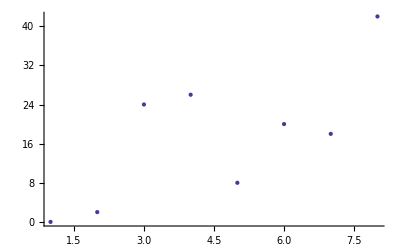

```mathematica
ListPlot[Sort[bad,FromDigits[Take[PadLeft[IntegerDigits[2^#1,3],6],6],3]<FromDigits[Take[PadLeft[IntegerDigits[2^#2,3],6],6],3]&]]
```

```mathematica
Place[x_,points_,mult_] := Module[
{angle=(2*Pi)/points},
{N[Cos[x*angle]],N[Sin[x*angle]]}* mult
]
```

```mathematica
points=Module[
{points=2*3^5},
Table[
Place[2^i,points,2],{i,bad}]
]
```

{{1.99983,0.025856},{1.99733,0.103381},{-1.97182,-0.334557},{-1.84151,-0.780272},{1.98331,0.257848},{1.73848,0.988783},{-0.909133,-1.78143},{0.696175,1.87492},{1.87038,0.70828},{0.245022,1.98493},{-0.0129283,-1.99996},{-0.321804,-1.97394},{0.0904677,1.99795},{-1.99983,-0.025856},{1.99733,0.103381},{1.98331,0.257848},{1.73848,0.988783},{0.977524,1.74483},{-0.909133,-1.78143},{-0.768352,-1.84652},{-0.0129283,-1.99996},{-1.77551,-0.920629},{-0.321804,-1.97394},{-1.97182,-0.334557},{-1.84151,-0.780272},{0.977524,1.74483},{0.696175,1.87492},{1.87038,0.70828},{0.245022,1.98493},{-0.768352,-1.84652},{-1.77551,-0.920629},{0.0904677,1.99795}}

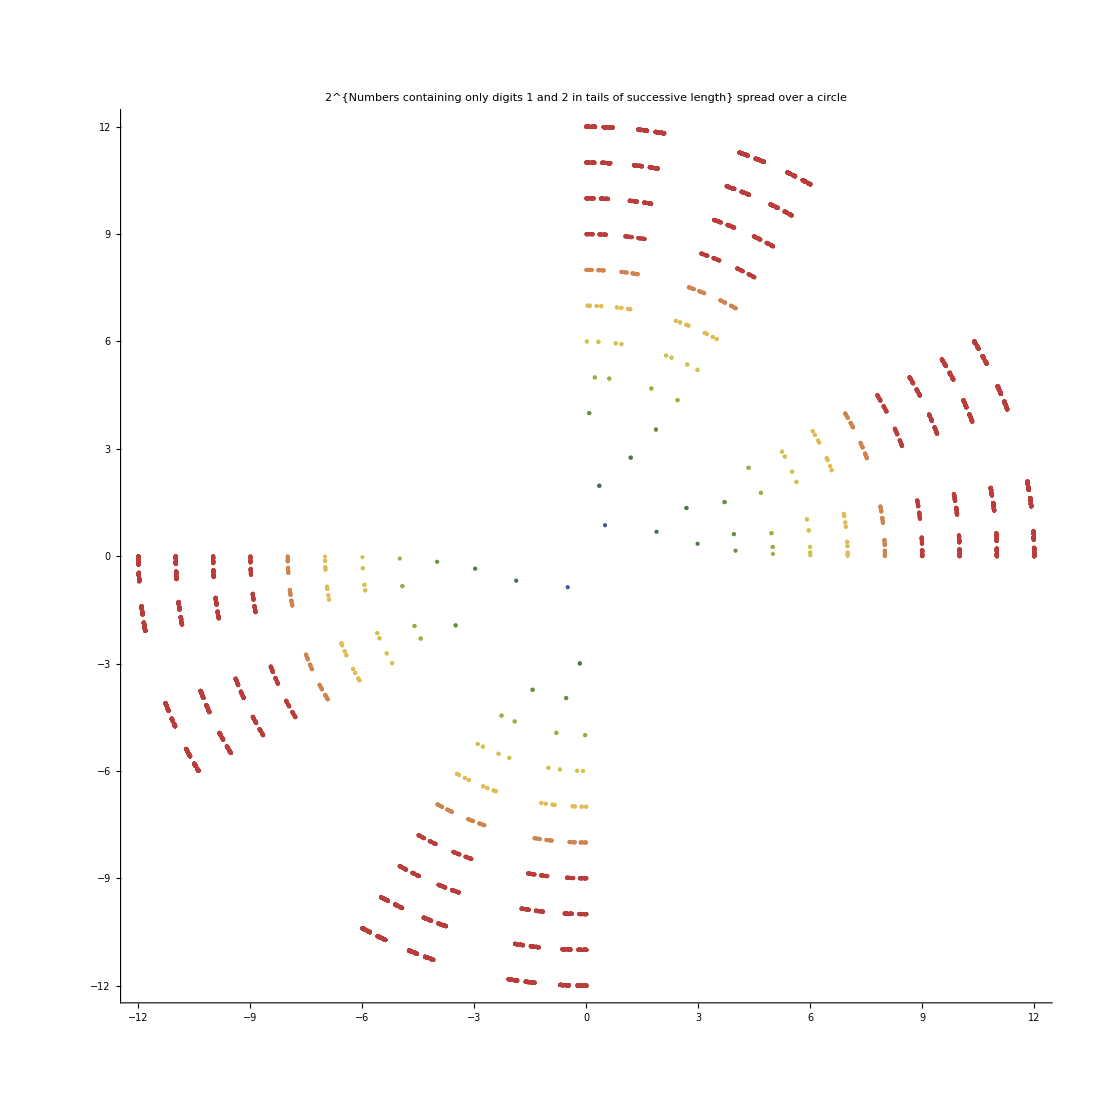

```mathematica
Module[{bad,points},
Monitor[
Show[
Table[
bad=Module[
{pow3,runLength,  x, valueTail, allTwos, result={}},
pow3=3^(max+1);
runLength=2 * 3^max;
Monitor[
For[x=0, x<runLength,x++,
valueTail=IntegerDigits[Mod[2^x,pow3],3];
If [!MemberQ[valueTail,2],
AppendTo[result,x];
]
],
{x, runLength}];
result
];
points=Module[
{count=2*3^max},
Table[
Place[2^i,count,max],{i,bad}]
];
ListPlot[points, PlotRange->All, AspectRatio->1, PlotStyle->ColorData["DarkRainbow"][max/10]]
,{max,1,12}
],
PlotLabel->"2^{Numbers containing only digits 1 and 2 in tails of successive length}\nspread over a circle"
],
max
]
]
```

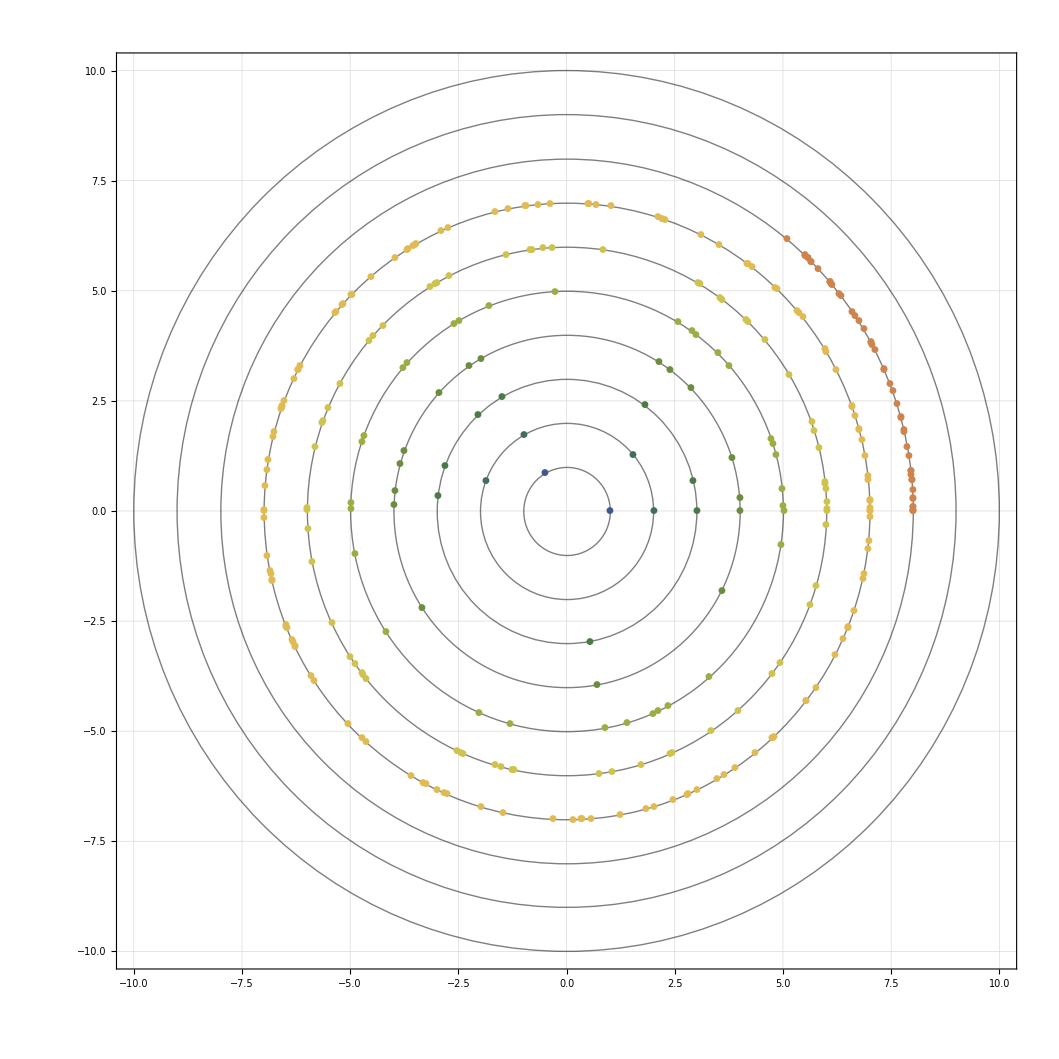

```mathematica
With[{MAX=10},
Module[{bad,points},
Monitor[
Show[
Table[
bad=Module[
{pow3,runLength,  x, valueTail, allTwos, result={}},
pow3=3^(max+1);
runLength=2 * 3^max;
Monitor[
For[x=0, x<runLength,x++,
valueTail=IntegerDigits[Mod[2^x,pow3],3];
If [!MemberQ[valueTail,2],
AppendTo[result,{x, valueTail}];
]
],
{x, runLength}];
result
];
points=Module[
{count=2*3^max,pow3=3^max},
Table[
With[
{place=Place[i[[1]],count,max]},
Tooltip[place,i[[2]]]
],{i,bad}]
];
Show[
Graphics[{PlotStyle->ColorData["DarkRainbow"][(MAX-max)/MAX],Opacity[0.5],Circle[{0,0},max]}],
ListPlot[points, AspectRatio->1, PlotStyle->ColorData["DarkRainbow"][max/MAX],PlotRange->All, PlotMarkers->Automatic]
]
,{max,1,MAX}
],
AspectRatio->1, GridLines->Automatic, Frame->True
],
max
]
]
]
```

```mathematica
Place2[x_,points_,mult_] := {x/points,mult}
```

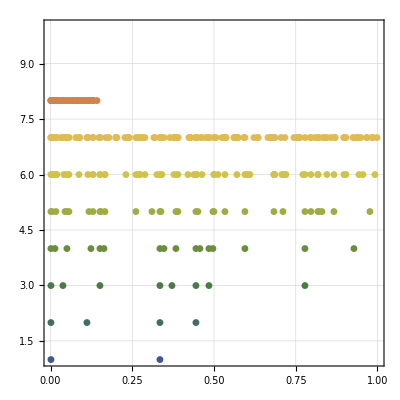

```mathematica
With[{MAX=10},
Module[{bad,points},
Monitor[
Show[
Table[
bad=Module[
{pow3,runLength,  x, valueTail, allTwos, result={}},
pow3=3^(max+1);
runLength=2 * 3^max;
Monitor[
For[x=0, x<runLength,x++,
valueTail=IntegerDigits[Mod[2^x,pow3],3];
If [!MemberQ[valueTail,2],
AppendTo[result,{x, valueTail}];
]
],
{x, runLength}];
result
];
points=Module[
{count=2*3^max,pow3=3^max},
Table[
With[
{place=Place2[i[[1]],count,max]},
Tooltip[place,i[[2]]]
],{i,bad}]
];
ListPlot[points, AspectRatio->1, PlotStyle->ColorData["DarkRainbow"][max/MAX],PlotRange->All, PlotMarkers->Automatic]
,{max,1,MAX}
],
AspectRatio->1, GridLines->Automatic, Frame->True
],
max
]
]
]
```

```mathematica
Module[{bad,points},
Monitor[
Show[
Table[
bad=Module[
{pow3,runLength,  x, valueTail, allTwos, result={}},
pow3=3^(max+1);
runLength=2 * 3^max;
Monitor[
For[x=0, x<runLength,x++,
valueTail=IntegerDigits[Mod[2^x,pow3],3];
If [!MemberQ[valueTail,2],
AppendTo[result,{x, valueTail}];
]
],
{x, runLength}];
result
];
points=Module[
{count=2*3^max,pow3=3^max},
Table[
With[
{place=Place2[i[[1]],count,max]},
Tooltip[place,i[[2]]]
],{i,bad}]
];
ListPlot[points, AspectRatio->1, PlotStyle->ColorData["DarkRainbow"][max/10],PlotRange->All, PlotMarkers->Automatic]
,{max,1,12}
],
AspectRatio->1, GridLines->Automatic, Frame->True
],
max
]
]
```

$Aborted

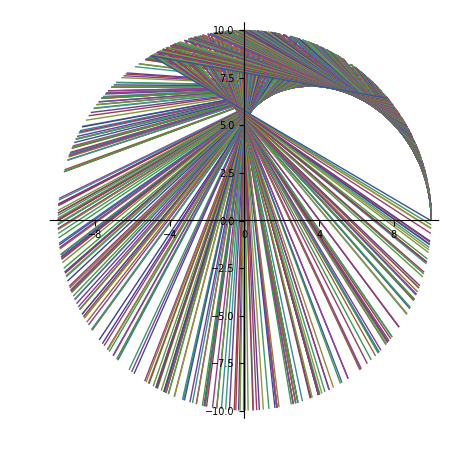

```mathematica
Module[
{max, values={}, pow3, runLength, valueTail,x},
For[max=0,max <12, max++,
pow3=3^(max+1);
runLength=2 * 3^max;
Monitor[
For[x=0, x<runLength,x++,
valueTail=IntegerDigits[Mod[2^x,pow3],3];
If [!MemberQ[valueTail,2],
AppendTo[values,{x, max}];
]
],x
]
];
values=Sort[values];
values = Split[values,#1[[1]]==#2[[1]]&];
values = Table[
Map[Place[#[[1]],2 * 3^#[[2]],10]&, elList],
{elList, values}];
(*values = Map[Map[Place[#[[1]],2 * 3^#[[2]],#[[2]]]&,#]&,values];*)
values=Select[values,Length[#]>2&];
ListLinePlot[values,AspectRatio->1]
]
```